```mathematica
(*两个平行带电线圈周围的电势*)
```

```mathematica
a=R^2+ρ^2+z^2+dist^2/4-dist*z;b=2ρ*R;c=R^2+ρ^2+z^2+dist^2/4+dist*z;d=2ρ*R;
Subscript[V, 1][ρ_,z_]:=1/(√(a^2-b^2))2 (√(a+b) EllipticK[-(2 b)/(a-b)]+√(a-b) EllipticK[(2 b)/(a+b)]);
Subscript[V, 2][ρ_,z_]:=-1/(√(c^2-d^2))2 (√(c+d) EllipticK[-(2 d)/(c-d)]+√(c-d) EllipticK[(2 d)/(c+d)]);
R=1;dist=R;
V[ρ_,z_]:=Subscript[V, 1][ρ,z]+Subscript[V, 2][ρ,z];
Plot3D[V[ρ,z],{ρ,0,2R},{z,-3R,3R},PlotRange->All,PlotPoints->50,AxesLabel->{"ρ","z","V"}]
```

-Graphics3D-

```mathematica
(*上线圈平面内的电势*)
```

```mathematica
Plot[V[ρ,z]/.z->0.5,{ρ,0,5R},PlotRange->{{0,5R},{0,50}},AxesOrigin->{0,0},AxesLabel->{"ρ","V"}]
```

-Graphics-

```mathematica
(*电势随z轴的分布*)
```

```mathematica
Plot[V[ρ,z]/.ρ->0,{z,-3R,3R},PlotRange->All,AxesOrigin->{0,0},AxesLabel->{"z","V"}]
```

-Graphics-

```mathematica
(*Subscript[z轴上的场强即E, z] 分布*)
```

```mathematica
field=-D[V[ρ,z],z]/.ρ->0;
Plot[field,{z,-3R,3R},PlotRange->All,AxesLabel->{"z","E"}]
```

-Graphics-

```mathematica
FindMaximum[V[ρ,z]/.ρ->0,{z,R}]
```

{2.19089,{z→0.837619}}

```mathematica
(*z轴的吸尘器*)
```

```mathematica
Integrate[field,{z,-1,1}]
```

```mathematica
(-8/(√5)+8/(√13)) π//N

Integrate[field,{z,x,-1}]
4/65 π (13 √5-5 √13+(65 √((5+4 (-1+x) x)^2))/(5+4 (-1+x) x)^(3/2)-(65 √((5+4 x (1+x))^2))/(5+4 x (1+x))^(3/2))
NSolve[4/65 π (13 √5-5 √13+(65 √((5+4 (-1+x) x)^2))/(5+4 (-1+x) x)^(3/2)-(65 √((5+4 x (1+x))^2))/(5+4 x (1+x))^(3/2))==4.269135324041176,x]
```

-4.26914

4/65 π (13 √5-5 √13+(65 √((5+4 (-1+x) x)^2))/(5+4 (-1+x) x)^(3/2)-(65 √((5+4 x (1+x))^2))/(5+4 x (1+x))^(3/2))

{{x→1.},{x→0.69481}}

```mathematica
NIntegrate[field,{z,-∞,-1}]
```

2.13457

```mathematica
(*过z轴的一个截面内的电势等高图*)
```

```mathematica
ContourPlot[V[ρ,z],{ρ,-3,3},{z,-1.5,1.5},PlotPoints->100,ContourShading->False,FrameLabel->{"ρ","z"},Contours->20]
```

-Graphics-

```mathematica
(*一个截面内的电场线*)
```

```mathematica
field=-D[V[ρ,z],ρ]-ⅈ*D[V[ρ,z],z];
dist=1.0;R=1.0;r1=0.003;r2=3.0;step=0.005;
p1={R,dist/2};p2={R,-dist/2};
forceline={};
Do[θ=ϕ;single={p1};Label[ss];p=Last[single];p=p+step*{Cos[θ],Sin[θ]};θ=Arg[field/.{ρ->p[[1]],z->p[[2]]}];If[(Norm[p-p1]>r1)∧(Norm[p-p2]>r1)∧(Norm[p]<r2),AppendTo[single,p];Goto[ss]];AppendTo[forceline,single],{ϕ,-π,π,π/10}]
g1=Show[Graphics[{Line/@forceline}]];
forceline={};
Do[θ=ϕ;single={p2};Label[ss];p=Last[single];p=p-step*{Cos[θ],Sin[θ]};θ=Arg[field/.{ρ->p[[1]],z->p[[2]]}];If[(Norm[p-p1]>r1)∧(Norm[p-p2]>r1)∧(Norm[p]<r2),AppendTo[single,p];Goto[ss]];AppendTo[forceline,single],{ϕ,-π,π,π/10.0}]
g2=Show[Graphics[{Line/@forceline}]];
Show[{g1,g2},AxesLabel->{"ρ","z"},PlotRange->{{0,r2},All},Axes->True,AxesOrigin->{0,0},AspectRatio->1]
```

-Graphics-

```mathematica
Clear[R,dist,field,p1,p2,r1,r2,step,forceline,single,θ,p,g1,g2]
```

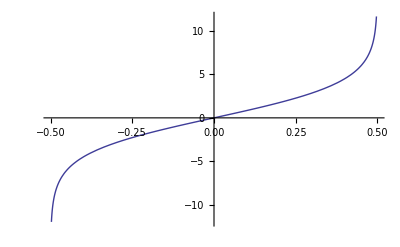

```mathematica
Plot[V[ρ,z]/.ρ->1,{z,-0.5,0.5}]
```

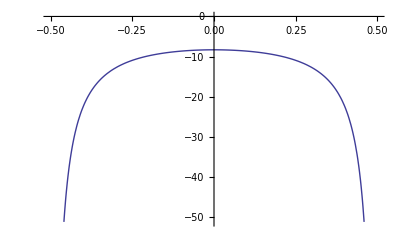

```mathematica
R=1;dist=1;
field=-D[V[ρ,z],z]/.ρ->1;
Plot[field,{z,-0.5,0.5},AxesOrigin->{0,0}]
```

```mathematica
(*证明：将R所有取值的圆环对的场强叠加一起来便得到了平行板电容器的场强*)
```

```mathematica
a=R^2+ρ^2+z^2+dist^2/4-dist*z;b=2ρ*R;c=R^2+ρ^2+z^2+dist^2/4+dist*z;d=2ρ*R;
Subscript[V, 1][ρ_,z_,R_]:=1/(√(a^2-b^2))2 (√(a+b) EllipticK[-(2 b)/(a-b)]+√(a-b) EllipticK[(2 b)/(a+b)]);
Subscript[V, 2][ρ_,z_,R_]:=-1/(√(c^2-d^2))2 (√(c+d) EllipticK[-(2 d)/(c-d)]+√(c-d) EllipticK[(2 d)/(c+d)]);
dist=1;
V[ρ_,z_,R_]:=Subscript[V, 1][ρ,z,R]+Subscript[V, 2][ρ,z,R];
field=-D[V[ρ,z,R],z]/.{ρ->0,z->0};
NIntegrate[field*R,{R,0,∞}]
```

```mathematica
(*=-4π*)
```

-12.5664